# A variational framework for near-optimal Bayesian quantum estimation of Gaussian states

This notebook contains symbolic calculations for estimation of a squeezing parameter encoded in the mean and/or covariances of a Gaussian state. 

In the following we will take a Gaussian prior (since rho_0 is not a Gaussian state the true S will never 

Last updated: 27/03/26.

## Zero mean

### B={1,Δx^2}

Use the quadratic centred basis B={1,Δx^2} with Δx^2=(x̂)^2-Tr(ρ_0(x̂)^2)

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ]; (*Gaussian prior*)

(*Subscript[ρ, 0] averages*)

avgx2ρ0=Integrate[x^2* p[θ]/.{x^2->Exp[-2 θ]Vxx},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

(*Gram matrix element*)

Gx2x2=Integrate[Expand[(x^2-avgx2ρ0)^2] p[θ]/.{x^4->3 (Vxx Exp[-2 θ])^2,x^2->Exp[-2 θ]Vxx},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

Gmat=({{1, 0}, {0, Gx2x2}});

Gmat//MatrixForm
```

ⅇ^(-2 μ0+2 σ0^2) Vxx

ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2

(1 | 0
0 | ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2)

b_i=Tr(ρ̄ B_i)

```mathematica
(*b vector*)
bx=Integrate[θ *(x^2-avgx2ρ0)* p[θ]/.{x^2->Exp[-2 θ]Vxx},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

bvec={μ0,bx};
```

-2 ⅇ^(-2 μ0+2 σ0^2) Vxx σ0^2

```mathematica
(*Solve*)
alpha=Simplify[Inverse[Gmat].bvec]//Simplify
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]
```

{μ0,(2 ⅇ^(2 μ0-2 σ0^2) σ0^2)/(Vxx-3 ⅇ^(4 σ0^2) Vxx)}

{μ0,-(ⅇ^(2 μ0) σ0^2)/Vxx}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL=λ-bvec.Inverse[Gmat].bvec//FullSimplify
```

μ0^2+σ0^2

σ0^2+(4 σ0^4)/(1-3 ⅇ^(4 σ0^2))

```mathematica
Normal[Series[MSL,{σ0,0,4}]]
```

σ0^2-2 σ0^4

### B={1,Δx_ϕ^2}

Use the linear basis B={1,Δx_ϕ^2} where Δx_ϕ^2=OverHat[x_ϕ]^2-Tr(ρ_0 OverHat[x_ϕ]^2).

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];

(*First moments*)
avgxϕ2=Integrate[(Expand[(x*Cos[ϕ]+q*Sin[ϕ])^2]) p[θ]/.{x^2->Exp[-2θ]Vxx,x*q->Vxp,x->0,q^2->Exp[2θ]*Vpp,q->0},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;

(*Gxϕ2xϕ2=Integrate[(Expand[((x*Cos[ϕ]+q*Sin[ϕ])^2-avgxϕ2)^2]) p[θ]/.{x^4->3*Exp[-4θ]*Vxx^2,x^3->0,x^2->Exp[-2θ]Vxx,x->0,q^4->3*Exp[4θ]*Vpp^2,q^3->0,q^2->Exp[2θ]*Vpp,q->0},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;*)

Gxϕ2xϕ2=Integrate[(Expand[((x*Cos[ϕ]+q*Sin[ϕ])^2-avgxϕ2)^2]) p[θ]/.{x^4->3*Exp[-4θ]*Vxx^2,x^3*q->3*Vxx*Exp[-2θ]*Vxp,x*q^3->3*Vpp*Exp[2θ]*Vxp,x^2*q^2->Vxx*Vpp+2 Vxp^2,x^3->0,x^2->Exp[-2θ]Vxx,x*q->Vxp,x->0,q^4->3*Exp[4θ]*Vpp^2,q^3->0,q^2->Exp[2θ]*Vpp,q->0},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;




(*Gram matrix *)
Gmat=({{1, 0}, {0, Gxϕ2xϕ2}})//Simplify;
Gmat//MatrixForm
```

(1 | 0
0 | ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2 Cos[ϕ]^4+8 ⅇ^(-2 μ0+2 σ0^2) Vxp Vxx Cos[ϕ]^3 Sin[ϕ]-2 (-3+ⅇ^(4 σ0^2)) Vpp Vxx Cos[ϕ]^2 Sin[ϕ]^2+8 ⅇ^(2 (μ0+σ0^2)) Vpp Vxp Cos[ϕ] Sin[ϕ]^3+ⅇ^(4 (μ0+σ0^2)) (-1+3 ⅇ^(4 σ0^2)) Vpp^2 Sin[ϕ]^4+2 Vxp^2 Sin[2 ϕ]^2)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
bxϕ2=Integrate[θ Expand[(x*Cos[ϕ]+q*Sin[ϕ])^2-avgxϕ2 ] p[θ]/.{x^2->Exp[-2θ]Vxx,x*q->Vxp,x->0,q^2->Exp[2θ]*Vpp,q->0},{θ,-Infinity,Infinity},Assumptions->σ0>0]  //Simplify  

bvec={b0,bxϕ2}//Simplify;
bvec
```

2 ⅇ^(-2 μ0+2 σ0^2) σ0^2 (-Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2)

{μ0,2 ⅇ^(-2 μ0+2 σ0^2) σ0^2 (-Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2)}

```mathematica
(* Alternatively, these can be derived by considering Subscript[x, ϕ] as a single quadrature with ((⟨x)_ϕ)^2⟩=V(θ)*)

V[θ_]:=Vxx Exp[-2θ] Cos[ϕ]^2+2 Vxp Cos[ϕ] Sin[ϕ]+Vpp Exp[2θ] Sin[ϕ]^2;

(*First moment*)
avgxϕ2=Integrate[V[θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;

(*Gram matrix element ((⟨x)_ϕ)^4⟩=3V(θ).b2 *)
Gxϕ2xϕ2=Integrate[3 V[θ]^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-avgxϕ2^2//Simplify;

Gmat={{1,0},{0,Gxϕ2xϕ2}}

(*b vector*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0];
bxϕ2=Integrate[θ (V[θ]-avgxϕ2) p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;
bvec={b0,bxϕ2}
```

{{1,0},{0,ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2 Cos[ϕ]^4+8 ⅇ^(-2 μ0+2 σ0^2) Vxp Vxx Cos[ϕ]^3 Sin[ϕ]-2 (-3+ⅇ^(4 σ0^2)) Vpp Vxx Cos[ϕ]^2 Sin[ϕ]^2+8 ⅇ^(2 (μ0+σ0^2)) Vpp Vxp Cos[ϕ] Sin[ϕ]^3+ⅇ^(4 (μ0+σ0^2)) (-1+3 ⅇ^(4 σ0^2)) Vpp^2 Sin[ϕ]^4+2 Vxp^2 Sin[2 ϕ]^2}}

{μ0,2 ⅇ^(-2 μ0+2 σ0^2) σ0^2 (-Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2)}

```mathematica
(*Solve to get Subscript[𝒮, 𝒱]*)
alpha=Simplify[Inverse[Gmat].bvec]//FullSimplify
(*Small sigma expansion*)
(*alphaSeries=Normal[Series[alpha,{σ0,0,2}]]//FullSimplify*)
```

{μ0,(2 ⅇ^(2 (μ0+σ0^2)) σ0^2 (-Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2))/(ⅇ^(4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2 Cos[ϕ]^4+8 ⅇ^(2 (μ0+σ0^2)) Vxp Vxx Cos[ϕ]^3 Sin[ϕ]+8 ⅇ^(6 μ0+2 σ0^2) Vpp Vxp Cos[ϕ] Sin[ϕ]^3+ⅇ^(8 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vpp^2 Sin[ϕ]^4+1/2 ⅇ^(4 μ0) (4 Vxp^2-(-3+ⅇ^(4 σ0^2)) Vpp Vxx) Sin[2 ϕ]^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  ;

MSL1xϕ2ZeroMean[ϕ_,μ0_,σ0_,Vxx_,Vpp_,Vxp_]=Simplify[λ-bvec.Inverse[Gmat].bvec];
```

```mathematica
MSL1xϕ2ZeroMean[ϕ,μ0,σ0,Vxx,Vpp,Vxp]
```

(σ0^2 (ⅇ^(4 σ0^2) Vxx^2 (-1+3 ⅇ^(4 σ0^2)-4 σ0^2) Cos[ϕ]^4+8 ⅇ^(2 (μ0+σ0^2)) Vxp Vxx Cos[ϕ]^3 Sin[ϕ]-2 ⅇ^(4 μ0) (-3+ⅇ^(4 σ0^2)) Vpp Vxx Cos[ϕ]^2 Sin[ϕ]^2+8 ⅇ^(6 μ0+2 σ0^2) Vpp Vxp Cos[ϕ] Sin[ϕ]^3+ⅇ^(4 μ0) (ⅇ^(4 (μ0+σ0^2)) Vpp^2 (-1+3 ⅇ^(4 σ0^2)-4 σ0^2) Sin[ϕ]^4+2 (Vxp^2+ⅇ^(4 σ0^2) Vpp Vxx σ0^2) Sin[2 ϕ]^2)))/(ⅇ^(4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2 Cos[ϕ]^4+8 ⅇ^(2 (μ0+σ0^2)) Vxp Vxx Cos[ϕ]^3 Sin[ϕ]-2 ⅇ^(4 μ0) (-3+ⅇ^(4 σ0^2)) Vpp Vxx Cos[ϕ]^2 Sin[ϕ]^2+8 ⅇ^(6 μ0+2 σ0^2) Vpp Vxp Cos[ϕ] Sin[ϕ]^3+ⅇ^(8 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vpp^2 Sin[ϕ]^4+2 ⅇ^(4 μ0) Vxp^2 Sin[2 ϕ]^2)

```mathematica
MSL1xϕ2ZeroMean[0,μ0,σ0,Vxx,Vpp,Vxp]//FullSimplify
MSL1xϕ2ZeroMean[π/2,μ0,σ0,Vxx,Vpp,Vxp]//FullSimplify
```

σ0^2+(4 σ0^4)/(1-3 ⅇ^(4 σ0^2))

σ0^2+(4 σ0^4)/(1-3 ⅇ^(4 σ0^2))

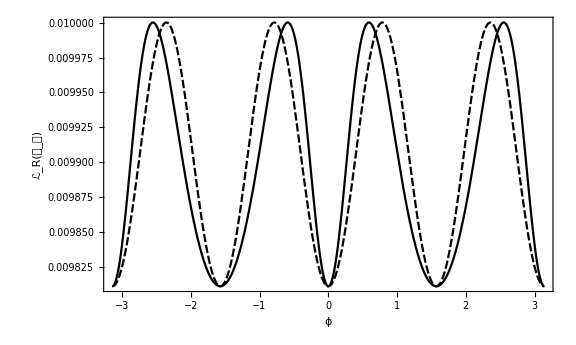

```mathematica
nμ0=0.1;
nσ0=0.1;

nVxx=0.5;
nVpp=0.5;
nVxp=0;

nr=0.1;

Plot[{MSL1xϕ2ZeroMean[ϕ,nμ0,nσ0,nVxx*Exp[-2nr],nVpp*Exp[2nr],nVxp],MSL1xϕ2ZeroMean[ϕ,nμ0,nσ0,nVxx*Exp[2nr],nVpp*Exp[-2nr],nVxp]},{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,π/2}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

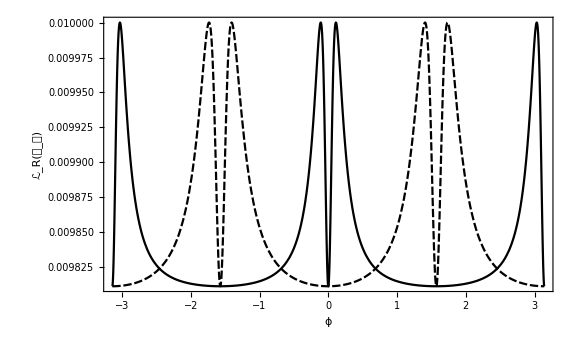

```mathematica
nr=1;

Plot[{MSL1xϕ2ZeroMean[ϕ,nμ0,nσ0,nVxx*Exp[-2nr],nVpp*Exp[2nr],nVxp],MSL1xϕ2ZeroMean[ϕ,nμ0,nσ0,nVxx*Exp[2nr],nVpp*Exp[-2nr],nVxp]},{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,π/2}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

Compare the O(σ_0^4) with the Classical Fisher information for zero-mean homodyne.
This gives the likelihood p(x_ϕ|θ)=𝒩(0,Var_ϕ(θ)) where Var_ϕ(θ)= V_xx e^(-2θ)(cos(ϕ))^2+V_pp e^(2θ)(sin(ϕ))^2

```mathematica
Normal@Series[MSL1xϕ2ZeroMean[ϕ,μ0,σ0,Vxx,Vpp,Vxp],{σ0,0,4}]
```

σ0^2-(2 σ0^4 (-ⅇ^(4 μ0) Vpp+Vxx+ⅇ^(4 μ0) Vpp Cos[2 ϕ]+Vxx Cos[2 ϕ])^2)/((-ⅇ^(4 μ0) Vpp-Vxx+ⅇ^(4 μ0) Vpp Cos[2 ϕ]-Vxx Cos[2 ϕ]-2 ⅇ^(2 μ0) Vxp Sin[2 ϕ])^2)

```mathematica
(* The CFI here comes purely from variance encoding CFI=(∂_θ Var(θ)^2)/2Var(θ)^2|_(θ->Subscript[μ, 0])*)

FisherHomodyneZeroMean[ϕ_,μ0_,Vxx_,Vpp_,Vxp_]:=Module[{var,dvar},
var=Vxx Exp[-2μ0] Cos[ϕ]^2+Vpp Exp[2μ0] Sin[ϕ]^2+2 Vxp Cos[ϕ] Sin[ϕ];
dvar=-2 Vxx Exp[-2μ0] Cos[ϕ]^2+2 Vpp Exp[2μ0] Sin[ϕ]^2;
dvar^2/(2 var^2)]

(*Verify against the series coefficient*)
Simplify[FisherHomodyneZeroMean[ϕ,μ0,Vxx,Vpp,Vxp]==(2 (-ⅇ^(4 μ0) Vpp+Vxx+ⅇ^(4 μ0) Vpp Cos[2 ϕ]+Vxx Cos[2 ϕ])^2)/((-ⅇ^(4 μ0) Vpp-Vxx+ⅇ^(4 μ0) Vpp Cos[2 ϕ]-Vxx Cos[2 ϕ]-2 ⅇ^(2 μ0) Vxp Sin[2 ϕ])^2)]
```

True

```mathematica
FisherHomodyneZeroMean[0,μ0,Vxx,Vpp,Vxp]//Simplify
FisherHomodyneZeroMean[π/2,μ0,Vxx,Vpp,Vxp]//Simplify
```

2

2

### B={1,Δx^2,Δp^2}

Use the quadratic centred basis B={1,Δx^2,Δp^2} with Δx^2=(x̂)^2-Tr(ρ_0(x̂)^2) and Δp^2=(p̂)^2-Tr(ρ_0(p̂)^2)

```mathematica
(*Choose a Gaussian prior for simple moments*)
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];

(*Subscript[ρ, 0] averages*)
avgx2ρ0=Integrate[x^2* p[θ]/.{x^2->Exp[-2 θ]Vxx},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify
avgp2ρ0=Integrate[q^2* p[θ]/.{q^2->Exp[2 θ]Vpp},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify


(*2x2 Gram matrix block*)

Gx2x2=Integrate[Expand[(x^2-avgx2ρ0)^2] p[θ]/.{x^4->3 (Vxx Exp[-2 θ])^2,x^2->Exp[-2 θ]Vxx},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

Gp2p2=Integrate[Expand[(q^2-avgp2ρ0)^2] p[θ]/.{q^4->3 (Vpp Exp[2 θ])^2,q^2->Exp[2 θ]Vpp},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

Gx2p2=Integrate[Expand[Vxx Vpp+2*Vxp^2-1/2-avgx2ρ0*avgp2ρ0] p[θ]/.{x^2->Exp[-2 θ]Vxx,q^2->Exp[2 θ]Vpp},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify


(*Build quadratic block*)
GmatBlock={{Gx2x2,Gx2p2},{Gx2p2,Gp2p2}}//FullSimplify;
GmatBlock//MatrixForm
```

ⅇ^(-2 μ0+2 σ0^2) Vxx

ⅇ^(2 (μ0+σ0^2)) Vpp

ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2

ⅇ^(4 (μ0+σ0^2)) (-1+3 ⅇ^(4 σ0^2)) Vpp^2

-1/2+2 Vxp^2-(-1+ⅇ^(4 σ0^2)) Vpp Vxx

(ⅇ^(-4 μ0+4 σ0^2) (-1+3 ⅇ^(4 σ0^2)) Vxx^2 | -1/2+2 Vxp^2-(-1+ⅇ^(4 σ0^2)) Vpp Vxx
-1/2+2 Vxp^2-(-1+ⅇ^(4 σ0^2)) Vpp Vxx | ⅇ^(4 (μ0+σ0^2)) (-1+3 ⅇ^(4 σ0^2)) Vpp^2)

b_i=Tr(ρ̄ B_i)

```mathematica
(*b vector*)
bx=Integrate[θ*(x^2-avgx2ρ0) p[θ]/.{x^2->Exp[-2 θ]Vxx},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify
bp=Integrate[θ*(q^2-avgp2ρ0) p[θ]/.{q^2->Exp[2 θ]Vpp},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify
bvec={bx,bp};
```

-2 ⅇ^(-2 μ0+2 σ0^2) Vxx σ0^2

2 ⅇ^(2 (μ0+σ0^2)) Vpp σ0^2

```mathematica
(*Solve*)
alpha=Simplify[Inverse[GmatBlock].bvec]
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]
```

{-(4 ⅇ^(2 (μ0+σ0^2)) Vpp σ0^2)/(1-4 Vxp^2+2 (-1+3 ⅇ^(8 σ0^2)) Vpp Vxx),(4 ⅇ^(-2 μ0+2 σ0^2) Vxx σ0^2)/(1-4 Vxp^2+2 (-1+3 ⅇ^(8 σ0^2)) Vpp Vxx)}

{-(4 ⅇ^(2 μ0) Vpp σ0^2)/(1-4 Vxp^2+4 Vpp Vxx),(4 ⅇ^(-2 μ0) Vxx σ0^2)/(1-4 Vxp^2+4 Vpp Vxx)}

```mathematica
alpha[[2]]/alpha[[1]]//Simplify

alphaSeries[[2]]/alphaSeries[[1]]//Simplify
```

-(ⅇ^(-4 μ0) Vxx)/Vpp

-(ⅇ^(-4 μ0) Vxx)/Vpp

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL=λ-(μ0^2+bvec.Inverse[GmatBlock].bvec)//FullSimplify
```

μ0^2+σ0^2

σ0^2-(16 ⅇ^(4 σ0^2) Vpp Vxx σ0^4)/(1-4 Vxp^2-2 Vpp Vxx+6 ⅇ^(8 σ0^2) Vpp Vxx)

```mathematica
Normal[Series[MSL,{σ0,0,4}]]
```

σ0^2-(16 Vpp Vxx σ0^4)/(1-4 Vxp^2+4 Vpp Vxx)

## Non-zero mean

### B={1,Δx,Δp}

Use the linear basis B={1,Δx,Δp} where Δx=x̂-Tr(ρ_0 x̂) and similarly for p.

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];
(*First moments*)
avgxρ0=Integrate[μx Exp[- θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgpρ0=Integrate[μp Exp[ θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]

(*Second moments*)
avgx2ρ0=Integrate[(Vxx+μx^2) Exp[-2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
avgp2ρ0=Integrate[(Vpp+μp^2) Exp[2 θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
(*Mixed moment*)
avgxpρ0=Integrate[μx μp p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]
(*Centered Gram elements*)
Gxx=avgx2ρ0-avgxρ0^2;
Gpp=avgp2ρ0-avgpρ0^2;
Gxp=avgxpρ0-avgxρ0*avgpρ0;
(*Build quadratic block*)
M={{Gxx,Gxp},{Gxp,Gpp}}//FullSimplify;
M//MatrixForm
```

ⅇ^(-μ0+σ0^2/2) μx

ⅇ^(μ0+σ0^2/2) μp

ⅇ^(-2 μ0+2 σ0^2) (Vxx+μx^2)

ⅇ^(2 (μ0+σ0^2)) (Vpp+μp^2)

μp μx

(ⅇ^(-2 μ0+σ0^2) (-μx^2+ⅇ^(σ0^2) (Vxx+μx^2)) | -((-1+ⅇ^(σ0^2)) μp μx)
-((-1+ⅇ^(σ0^2)) μp μx) | ⅇ^(2 μ0+σ0^2) (-μp^2+ⅇ^(σ0^2) (Vpp+μp^2)))

```mathematica
(*b vector*)
bx=Integrate[θ μx Exp[- θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-μ0*avgxρ0//Simplify
bp=Integrate[θ μp Exp[ θ] p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]-μ0*avgpρ0 // Simplify
b={bx,bp};
(*Solve*)
alpha=Simplify[Inverse[M].b]//FullSimplify
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]//FullSimplify
```

-ⅇ^(-μ0+σ0^2/2) μx σ0^2

ⅇ^(μ0+σ0^2/2) μp σ0^2

{-(ⅇ^(μ0+σ0^2/2) (μp^2-2 ⅇ^(σ0^2) μp^2+ⅇ^(2 σ0^2) (Vpp+μp^2)) μx σ0^2)/(-μp^2 μx^2+2 ⅇ^(σ0^2) μp^2 μx^2+ⅇ^(4 σ0^2) (Vpp+μp^2) (Vxx+μx^2)-ⅇ^(3 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2)),(ⅇ^(-μ0+σ0^2/2) μp (μx^2-2 ⅇ^(σ0^2) μx^2+ⅇ^(2 σ0^2) (Vxx+μx^2)) σ0^2)/(-μp^2 μx^2+2 ⅇ^(σ0^2) μp^2 μx^2+ⅇ^(4 σ0^2) (Vpp+μp^2) (Vxx+μx^2)-ⅇ^(3 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2))}

{-(ⅇ^μ0 μx σ0^2)/Vxx,(ⅇ^-μ0 μp σ0^2)/Vpp}

```mathematica
Series[alpha[[2]]/alpha[[1]],{σ0,0,4}]
```

-(ⅇ^(-2 μ0) Vxx μp)/(Vpp μx)-(ⅇ^(-2 μ0) μp (-Vxx μp^2+Vpp μx^2) σ0^4)/(Vpp^2 μx)+O[σ0]^5

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL=λ-b.Inverse[M].b//FullSimplify
```

μ0^2+σ0^2

μ0^2+σ0^2+(ⅇ^(σ0^2) (-2 μp^2 μx^2+4 ⅇ^(σ0^2) μp^2 μx^2-ⅇ^(2 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2)) σ0^4)/(-μp^2 μx^2+2 ⅇ^(σ0^2) μp^2 μx^2+ⅇ^(4 σ0^2) (Vpp+μp^2) (Vxx+μx^2)-ⅇ^(3 σ0^2) (Vxx μp^2+(Vpp+2 μp^2) μx^2))

```mathematica
(*MSL for a squeeed displaced probe*)

Normal[Series[MSL/.{Vxx->Exp[2r],Vpp->Exp[-2r],μx->μ*Cos[ϕ],μp->μ*Sin[ϕ]},{σ0,0,4}]]//FullSimplify
```

μ0^2+σ0^2-ⅇ^(-2 r) μ^2 σ0^4 (Cos[ϕ]^2+ⅇ^(4 r) Sin[ϕ]^2)

```mathematica
Mod[(ϕ/.Maximize[{ⅇ^(-2 r) (Cos[ϕ]^2+ⅇ^(4 r) Sin[ϕ]^2)/.{r->12},0<=ϕ<2π},ϕ][[2,1]]) ,π](*MSL Maximised at ϕ=π/2+kπ*)
```

π/2

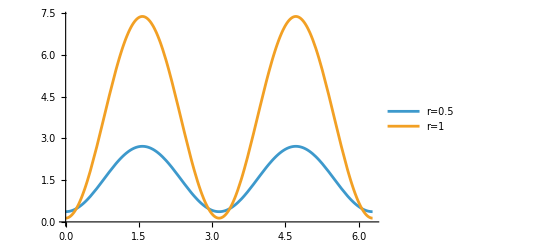

```mathematica
Plot[Evaluate@Table[ⅇ^(-2 r) (Cos[ϕ]^2+ⅇ^(4 r) Sin[ϕ]^2),{r,{0.5,1}}],{ϕ,0,2π},PlotLegends->Table[StringForm["r=``",r],{r,{0.5,1}}]]
```

```mathematica
InfoGainSqueezedDisplaced[μ0_,σ0_,μ_,ϕ_,r_]=λ-MSL/.{Vxx->Exp[2r],Vpp->Exp[-2r],μx->μ*Cos[ϕ],μp->μ*Sin[ϕ]}//Simplify
```

(ⅇ^(σ0^2) μ^2 σ0^4 (ⅇ^(4 r+2 σ0^2) Sin[ϕ]^2+Cos[ϕ]^2 (ⅇ^(2 σ0^2)+2 ⅇ^(2 r) (-1+ⅇ^(σ0^2))^2 μ^2 Sin[ϕ]^2)))/(ⅇ^(2 r+3 σ0^2) (ⅇ^(σ0^2)+ⅇ^(2 r) (-1+ⅇ^(σ0^2)) μ^2 Sin[ϕ]^2)+(-1+ⅇ^(σ0^2)) μ^2 Cos[ϕ]^2 (ⅇ^(3 σ0^2)+ⅇ^(2 r) (-1+ⅇ^(σ0^2))^2 (1+ⅇ^(σ0^2)) μ^2 Sin[ϕ]^2))

```mathematica
Mod[(ϕ/.Maximize[{InfoGainSqueezedDisplaced[1,1,1,ϕ,1],0<=ϕ<2π},ϕ][[2,1]]) ,π](*MSL Maximised at ϕ=π/2+kπ*)
```

π/2

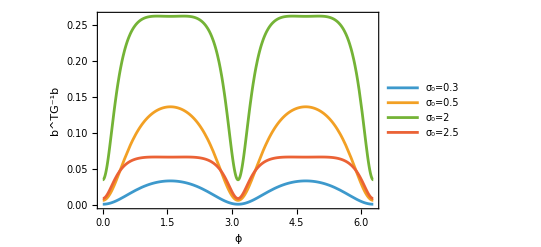

```mathematica
σ0list={0.3,0.5,2,2.5};

Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,1,ϕ,1],{σ0,σ0list}],{ϕ,0,2π},PlotLegends->Table[StringForm["σ_0=``",σ0],{σ0,σ0list}],Frame->True,FrameLabel->{"ϕ","b^TG^-1b"}]

(*σ0list={3,3.5,4};

Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,1,ϕ,1],{σ0,σ0list}],{ϕ,0,2π},PlotLegends->Table[StringForm["σ_0=``",σ0],{σ0,σ0list}],Frame->True,FrameLabel->{"ϕ","b^TG^-1b"}]*)
```

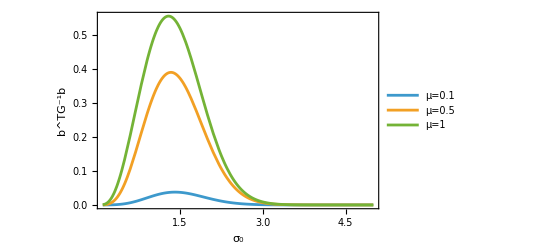

```mathematica
Plot[Evaluate@Table[InfoGainSqueezedDisplaced[1,σ0,μ,π/2,1],{μ,{0.1,0.5,1}}],{σ0,0.1,5},PlotLegends->Table[StringForm["μ=``",μ],{μ,{0.1,0.5,1}}],Frame->True,FrameLabel->{"σ_0","b^TG^-1b"},PlotRange->All]
```

### B={1,Δx_ϕ}

Use the linear basis B={1,Δx_ϕ} where Δx_ϕ=OverHat[x_ϕ]-Tr(ρ_0 OverHat[x_ϕ]).

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];

(*First moments*)
avgxϕ0=Integrate[(x*Cos[ϕ]+q*Sin[ϕ] )p[θ]/.{x->x0*Exp[-θ],q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]

Gxϕxϕ=Integrate[(Expand[(x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0)^2]) p[θ]/.{x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;


(*Gram matrix *)
Gmat=({{1, 0}, {0, Gxϕxϕ}})//Simplify;
Gmat//MatrixForm
```

ⅇ^(-μ0+σ0^2/2) (x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ])

(1 | 0
0 | ⅇ^(-2 μ0+σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) Cos[ϕ]^2+ⅇ^(2 μ0+σ0^2) ((-1+ⅇ^(σ0^2)) p0^2+ⅇ^(σ0^2) Vpp) Sin[ϕ]^2-(-1+ⅇ^(σ0^2)) p0 x0 Sin[2 ϕ])

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
bxϕ=Integrate[θ (x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0 ) p[θ]/.{x->x0*Exp[-θ],q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0] ; //Simplify  

bvec={b0,bxϕ}//Simplify;
bvec
```

{μ0,ⅇ^(-μ0+σ0^2/2) σ0^2 (-x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ])}

```mathematica
(*Solve*)
alpha=Simplify[Inverse[Gmat].bvec]//FullSimplify
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]//FullSimplify
```

{μ0,(ⅇ^(μ0+σ0^2/2) σ0^2 (-x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ]))/(ⅇ^(σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) Cos[ϕ]^2+ⅇ^(4 μ0+σ0^2) (-p0^2+ⅇ^(σ0^2) (p0^2+Vpp)) Sin[ϕ]^2-ⅇ^(2 μ0) (-1+ⅇ^(σ0^2)) p0 x0 Sin[2 ϕ])}

{μ0,(ⅇ^μ0 σ0^2 (-x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ]))/(Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL1xϕ[ϕ_,μ0_,σ0_,x0_,p0_,Vxx_,Vpp_]=λ-bvec.Inverse[Gmat].bvec//FullSimplify
```

μ0^2+σ0^2

σ0^2-(ⅇ^(σ0^2) σ0^4 (x0 Cos[ϕ]-ⅇ^(2 μ0) p0 Sin[ϕ])^2)/(ⅇ^(σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) Cos[ϕ]^2+ⅇ^(4 μ0+σ0^2) (-p0^2+ⅇ^(σ0^2) (p0^2+Vpp)) Sin[ϕ]^2-ⅇ^(2 μ0) (-1+ⅇ^(σ0^2)) p0 x0 Sin[2 ϕ])

```mathematica
(* Check for small prior widths*)
```

```mathematica
Normal@Series[MSL1xϕ[ϕ,μ0,σ0,x0,p0,Vxx,Vpp],{σ0,0,4}]
```

σ0^2-(σ0^4 (x0 Cos[ϕ]-ⅇ^(2 μ0) p0 Sin[ϕ])^2)/(Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2)

```mathematica
Solve[D[(σ0^4 (x0 Cos[ϕ]-ⅇ^(2 μ0) p0 Sin[ϕ])^2)/(Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2),ϕ]==0,ϕ]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-ArcCos[-(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→ArcCos[-(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→-ArcCos[(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→ArcCos[(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→-ArcCos[-(ⅇ^(2 μ0) Vpp x0)/(√(p0^2 Vxx^2+ⅇ^(4 μ0) Vpp^2 x0^2))]},{ϕ→ArcCos[-(ⅇ^(2 μ0) Vpp x0)/(√(p0^2 Vxx^2+ⅇ^(4 μ0) Vpp^2 x0^2))]},{ϕ→-ArcCos[(ⅇ^(2 μ0) Vpp x0)/(√(p0^2 Vxx^2+ⅇ^(4 μ0) Vpp^2 x0^2))]},{ϕ→ArcCos[(ⅇ^(2 μ0) Vpp x0)/(√(p0^2 Vxx^2+ⅇ^(4 μ0) Vpp^2 x0^2))]}}

```mathematica
(* This matches the linear part of the QFI (see section at end)*)

((x0 Cos[ϕ]-ⅇ^(2 μ0) p0 Sin[ϕ])^2)/(Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2)/.ϕ->ArcTan[(-ⅇ^(-2 μ0) p0 Vxx)/(Vpp x0)]//Expand//FullSimplify
```

p0^2/Vpp+x0^2/Vxx

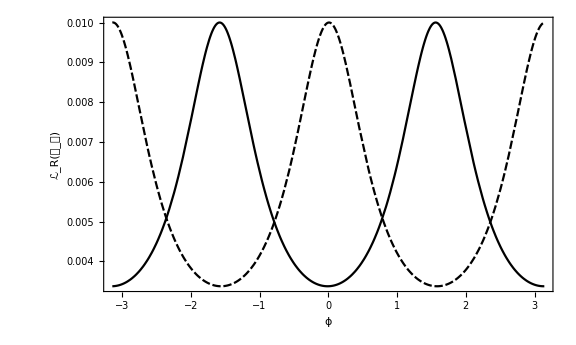

```mathematica
nμ0=0;
nσ0=0.1;
(*nx0=0.1;
np0=0.5;*)
nVxx=0.5;
nVpp=0.5;


Plot[{MSL1xϕ[ϕ,nμ0,nσ0,10,0.1,nVxx,nVpp],MSL1xϕ[ϕ,nμ0,nσ0,0.1,10,nVxx,nVpp]},{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,0,π/2,π/4}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

Determine the stationary points of the MSL w.r.t ϕ

```mathematica
Solve[D[MSL1xϕ[ϕ,μ0,σ0,x0,p0,Vxx,Vpp],ϕ]==0,ϕ]//FullSimplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→-ArcCos[-(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→ArcCos[-(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→-ArcCos[(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→ArcCos[(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]},{ϕ→-ArcCos[-(ⅇ^(2 μ0+σ0^2) x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2]))/(√(ⅇ^(4 μ0) ((-1+ⅇ^(σ0^2))^2 p0^2+ⅇ^(2 σ0^2) Vpp)^2 x0^2+p0^2 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2))^2))]},{ϕ→ArcCos[-(ⅇ^(2 μ0+σ0^2) x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2]))/(√(ⅇ^(4 μ0) ((-1+ⅇ^(σ0^2))^2 p0^2+ⅇ^(2 σ0^2) Vpp)^2 x0^2+p0^2 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2))^2))]},{ϕ→-ArcCos[(ⅇ^(2 μ0+σ0^2) x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2]))/(√(ⅇ^(4 μ0) ((-1+ⅇ^(σ0^2))^2 p0^2+ⅇ^(2 σ0^2) Vpp)^2 x0^2+p0^2 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2))^2))]},{ϕ→ArcCos[(ⅇ^(2 μ0+σ0^2) x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2]))/(√(ⅇ^(4 μ0) ((-1+ⅇ^(σ0^2))^2 p0^2+ⅇ^(2 σ0^2) Vpp)^2 x0^2+p0^2 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2))^2))]}}

```mathematica
(* When Subscript[x, 0]=0 we expect that homodyne angle is ϕ=π/2.*)

ArcCos[(ⅇ^(2 μ0) p0)/(√(ⅇ^(4 μ0) p0^2+x0^2))]/.{μ0->0.1,σ0->0.1,x0->0,p0->1,Vxx->0.5,Vpp->0.5}//N

(*This is therefore a maxima*)
```

0.

```mathematica
(*The minima are therefore *)

ArcCos[(-ⅇ^(2 μ0+σ0^2) x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2]))/(√(ⅇ^(4 μ0) ((-1+ⅇ^(σ0^2))^2 p0^2+ⅇ^(2 σ0^2) Vpp)^2 x0^2+p0^2 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2))^2))]/.{μ0->0.1,σ0->0.1,x0->0,p0->1,Vxx->0.5,Vpp->0.5}
```

1.5708

```mathematica
(*Rewrite using tan*)

ArcTan[(p0 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2)))/(-ⅇ^(2 μ0+σ0^2) x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2]))]/.{μ0->0.1,σ0->0.1,x0->0.0001,p0->1,Vxx->0.5,Vpp->0.5}
```

-1.57067

```mathematica
(* For small prior width this becomes*)
Series[(ⅇ^(-2 μ0-σ0^2) p0 (x0^2-2 ⅇ^(σ0^2) x0^2+ⅇ^(2 σ0^2) (Vxx+x0^2)))/(x0 (-2 p0^2+(2 p0^2+Vpp) Cosh[σ0^2]+Vpp Sinh[σ0^2])),{σ0,0,2}]
```

(ⅇ^(-2 μ0) p0 Vxx)/(Vpp x0)+O[σ0]^3

### B={1,Δx_ϕ^2}

Use the linear basis B={1,Δx_ϕ^2} where Δx_ϕ^2=OverHat[x_ϕ]^2-Tr(ρ_0 OverHat[x_ϕ]^2).

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];

(*First moments*)
avgxϕ2=Integrate[(Expand[(x*Cos[ϕ]+q*Sin[ϕ])^2]) p[θ]/.{x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;

Gxϕ2xϕ2=Integrate[(Expand[((x*Cos[ϕ]+q*Sin[ϕ])^2-avgxϕ2p)^2]) p[θ]/.{x^4->Exp[-4θ]*(x0^4+6*x0^2*Vxx+3*Vxx^2),x^3->Exp[-3θ]*(x0^3+3*x0*Vxx),x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^4->Exp[4θ]*(p0^4+6*p0^2*Vpp+3*Vpp^2),q^3->Exp[3θ]*(p0^3+3*p0*Vpp),q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]/.avgxϕ2p->avgxϕ2 //Simplify;



(*Gram matrix *)
Gmat=({{1, 0}, {0, Gxϕ2xϕ2}})//Simplify;
Gmat//MatrixForm
```

(1 | 0
0 | ⅇ^(-4 μ0+4 σ0^2) ((-1+3 ⅇ^(4 σ0^2)) Vxx^2+2 (-1+3 ⅇ^(4 σ0^2)) Vxx x0^2+(-1+ⅇ^(4 σ0^2)) x0^4) Cos[ϕ]^4+8 ⅇ^(-2 μ0+2 σ0^2) p0 Vxx x0 Cos[ϕ]^3 Sin[ϕ]-2 ((-3+ⅇ^(4 σ0^2)) Vpp (Vxx+x0^2)+p0^2 ((-3+ⅇ^(4 σ0^2)) Vxx+(-1+ⅇ^(4 σ0^2)) x0^2)) Cos[ϕ]^2 Sin[ϕ]^2+8 ⅇ^(2 (μ0+σ0^2)) p0 Vpp x0 Cos[ϕ] Sin[ϕ]^3+ⅇ^(4 (μ0+σ0^2)) ((-1+ⅇ^(4 σ0^2)) p0^4+2 (-1+3 ⅇ^(4 σ0^2)) p0^2 Vpp+(-1+3 ⅇ^(4 σ0^2)) Vpp^2) Sin[ϕ]^4)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
bxϕ2=Integrate[θ Expand[(x*Cos[ϕ]+q*Sin[ϕ])^2-avgxϕ2p ] p[θ]/.{x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0] /.avgxϕ2p->avgxϕ2 //Simplify  

bvec={b0,bxϕ2}//Simplify;
bvec
```

2 ⅇ^(-2 μ0+2 σ0^2) σ0^2 (-((Vxx+x0^2) Cos[ϕ]^2)+ⅇ^(4 μ0) (p0^2+Vpp) Sin[ϕ]^2)

{μ0,2 ⅇ^(-2 μ0+2 σ0^2) σ0^2 (-((Vxx+x0^2) Cos[ϕ]^2)+ⅇ^(4 μ0) (p0^2+Vpp) Sin[ϕ]^2)}

```mathematica
(*Solve*)
alpha=Simplify[Inverse[Gmat].bvec]//FullSimplify
(*Small sigma expansion*)
(*alphaSeries=Normal[Series[alpha,{σ0,0,2}]]//FullSimplify*)
```

{μ0,(2 ⅇ^(2 (μ0+σ0^2)) σ0^2 (-((Vxx+x0^2) Cos[ϕ]^2)+ⅇ^(4 μ0) (p0^2+Vpp) Sin[ϕ]^2))/(ⅇ^(4 σ0^2) (-(Vxx+x0^2)^2+ⅇ^(4 σ0^2) (3 Vxx^2+6 Vxx x0^2+x0^4)) Cos[ϕ]^4+8 ⅇ^(2 (μ0+σ0^2)) p0 Vxx x0 Cos[ϕ]^3 Sin[ϕ]+2 ⅇ^(4 μ0) (3 p0^2 Vxx+3 Vpp Vxx+p0^2 x0^2+3 Vpp x0^2-ⅇ^(4 σ0^2) (p0^2+Vpp) (Vxx+x0^2)) Cos[ϕ]^2 Sin[ϕ]^2+8 ⅇ^(6 μ0+2 σ0^2) p0 Vpp x0 Cos[ϕ] Sin[ϕ]^3+ⅇ^(8 μ0+4 σ0^2) (-(p0^2+Vpp)^2+ⅇ^(4 σ0^2) (p0^4+6 p0^2 Vpp+3 Vpp^2)) Sin[ϕ]^4)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0]  

MSL1xϕ2[ϕ_,μ0_,σ0_,x0_,p0_,Vxx_,Vpp_]=Simplify[λ-bvec.Inverse[Gmat].bvec];
```

μ0^2+σ0^2

```mathematica
Normal@Series[MSL1xϕ2[ϕ,μ0,σ0,x0,p0,Vxx,Vpp],{σ0,0,4}]
```

σ0^2-(2 σ0^4 ((Vxx+x0^2) Cos[ϕ]^2-ⅇ^(4 μ0) (p0^2+Vpp) Sin[ϕ]^2)^2)/((Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2) (Vxx Cos[ϕ]^2+2 x0^2 Cos[ϕ]^2+4 ⅇ^(2 μ0) p0 x0 Cos[ϕ] Sin[ϕ]+2 ⅇ^(4 μ0) p0^2 Sin[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2))

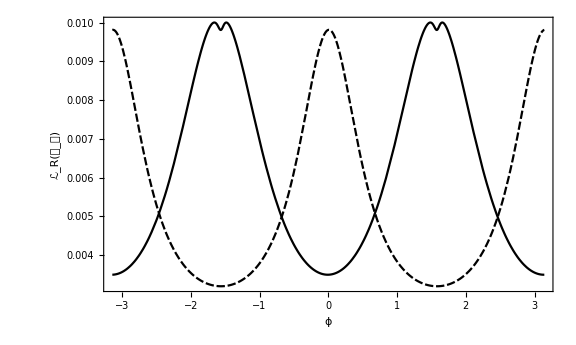

```mathematica
nμ0=0.1;
nσ0=0.1;
(*nx0=0.1;
np0=0.5;*)
nVxx=0.5;
nVpp=0.5;


Plot[{MSL1xϕ2[ϕ,nμ0,nσ0,10,0.1,nVxx,nVpp],MSL[ϕ,nμ0,nσ0,0.1,10,nVxx,nVpp]},{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,π/2}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

```mathematica
Solve[D[2 σ0^4 ((Vxx+x0^2) Cos[ϕ]^2-ⅇ^(4 μ0) (p0^2+Vpp) Sin[ϕ]^2)^2,ϕ]==0,ϕ]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→0},{ϕ→-π/2},{ϕ→π/2},{ϕ→-ArcCos[-(ⅇ^(2 μ0) √(p0^2+Vpp))/(√(ⅇ^(4 μ0) p0^2+ⅇ^(4 μ0) Vpp+Vxx+x0^2))]},{ϕ→ArcCos[-(ⅇ^(2 μ0) √(p0^2+Vpp))/(√(ⅇ^(4 μ0) p0^2+ⅇ^(4 μ0) Vpp+Vxx+x0^2))]},{ϕ→-ArcCos[(ⅇ^(2 μ0) √(p0^2+Vpp))/(√(ⅇ^(4 μ0) p0^2+ⅇ^(4 μ0) Vpp+Vxx+x0^2))]},{ϕ→ArcCos[(ⅇ^(2 μ0) √(p0^2+Vpp))/(√(ⅇ^(4 μ0) p0^2+ⅇ^(4 μ0) Vpp+Vxx+x0^2))]}}

```mathematica
√(ⅇ^(4 μ0) p0^2+ⅇ^(4 μ0) Vpp+Vxx+x0^2-(ⅇ^(2 μ0) √(p0^2+Vpp))^2)//Simplify
```

√(Vxx+x0^2)

```mathematica
-ArcTan[(√(Vxx+x0^2))/(ⅇ^(2 μ0) √(p0^2+Vpp))]/.{μ0->0.1,σ0->0.1,x0->0.1,p0->0.5,Vxx->0.5,Vpp->0.5}
```

-0.593848

### B={1,Δx_ϕ,Δx_ϕ^2}

Use the basis B={1,Δx_ϕ,Δx_ϕ^2} where Δx_ϕ=OverHat[x_ϕ]-Tr(ρ_0 OverHat[x_ϕ]).

```mathematica
p[θ_]:=PDF[NormalDistribution[μ0,σ0],θ];

(*First moments*)
avgxϕ0=Integrate[(x*Cos[ϕ]+q*Sin[ϕ] )p[θ]/.{x->x0*Exp[-θ],q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]

Gxϕxϕ=Integrate[(Expand[(x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0)^2]) p[θ]/.{x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify;

Gxϕ2xϕ2=Integrate[(Expand[(x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0p)^4]) p[θ]/.{x^4->Exp[-4θ]*(x0^4+6*x0^2*Vxx+3*Vxx^2),x^3->Exp[-3θ]*(x0^3+3*x0*Vxx),x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^4->Exp[4θ]*(p0^4+6*p0^2*Vpp+3*Vpp^2),q^3->Exp[3θ]*(p0^3+3*p0*Vpp),q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]/.avgxϕ0p->avgxϕ0 //Simplify;


(*Gram matrix *)
Gmat=({{1, 0, Gxϕxϕ}, {0, Gxϕxϕ, 0}, {Gxϕxϕ, 0, Gxϕ2xϕ2}})//Simplify;
Gmat//MatrixForm
```

ⅇ^(-μ0+σ0^2/2) (x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ])

(1 | 0 | ⅇ^(-2 μ0+σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) Cos[ϕ]^2+ⅇ^(2 μ0+σ0^2) ((-1+ⅇ^(σ0^2)) p0^2+ⅇ^(σ0^2) Vpp) Sin[ϕ]^2-(-1+ⅇ^(σ0^2)) p0 x0 Sin[2 ϕ]
0 | ⅇ^(-2 μ0+σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) Cos[ϕ]^2+ⅇ^(2 μ0+σ0^2) ((-1+ⅇ^(σ0^2)) p0^2+ⅇ^(σ0^2) Vpp) Sin[ϕ]^2-(-1+ⅇ^(σ0^2)) p0 x0 Sin[2 ϕ] | 0
ⅇ^(-2 μ0+σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) Cos[ϕ]^2+ⅇ^(2 μ0+σ0^2) ((-1+ⅇ^(σ0^2)) p0^2+ⅇ^(σ0^2) Vpp) Sin[ϕ]^2-(-1+ⅇ^(σ0^2)) p0 x0 Sin[2 ϕ] | 0 | ⅇ^(-4 μ0+2 σ0^2) (-3 x0^4+6 ⅇ^(σ0^2) x0^2 (Vxx+x0^2)-4 ⅇ^(3 σ0^2) x0^2 (3 Vxx+x0^2)+ⅇ^(6 σ0^2) (3 Vxx^2+6 Vxx x0^2+x0^4)) Cos[ϕ]^4-4 ⅇ^(-2 μ0+σ0^2) (-1+ⅇ^(σ0^2)) p0 x0 (3 (-1+ⅇ^(2 σ0^2)+ⅇ^(3 σ0^2)) Vxx+ⅇ^(σ0^2) (-2+ⅇ^(σ0^2)+ⅇ^(2 σ0^2)) x0^2) Cos[ϕ]^3 Sin[ϕ]-4 ⅇ^(2 μ0+σ0^2) (-1+ⅇ^(σ0^2)) p0 (-2 ⅇ^(σ0^2) p0^2-3 Vpp+ⅇ^(2 σ0^2) (p0^2+3 Vpp)+ⅇ^(3 σ0^2) (p0^2+3 Vpp)) x0 Cos[ϕ] Sin[ϕ]^3+ⅇ^(4 μ0+2 σ0^2) ((-3+6 ⅇ^(σ0^2)-4 ⅇ^(3 σ0^2)+ⅇ^(6 σ0^2)) p0^4+6 ⅇ^(σ0^2) (1-2 ⅇ^(2 σ0^2)+ⅇ^(5 σ0^2)) p0^2 Vpp+3 ⅇ^(6 σ0^2) Vpp^2) Sin[ϕ]^4+3/2 (p0^2 ((1-2 ⅇ^(σ0^2)+ⅇ^(3 σ0^2)) Vxx+(-1+ⅇ^(σ0^2))^2 (1+2 ⅇ^(σ0^2)) x0^2)+Vpp (Vxx+(1-2 ⅇ^(σ0^2)+ⅇ^(3 σ0^2)) x0^2)) Sin[2 ϕ]^2)

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0] ;
bxϕ=Integrate[θ (x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0 ) p[θ]/.{x->x0*Exp[-θ],q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0] ; //Simplify  
bxϕ2=Integrate[θ Expand[(x*Cos[ϕ]+q*Sin[ϕ]-avgxϕ0p )^2] p[θ]/.{x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],q^2->Exp[2θ]*(p0^2+Vpp),q->p0*Exp[θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0] /.avgxϕ0p->avgxϕ0 //Simplify  

bvec={b0,bxϕ,bxϕ2}//Simplify;
bvec
```

ⅇ^(-2 μ0+σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) (μ0-2 σ0^2) Cos[ϕ]^2-2 ⅇ^(σ0^2) p0 x0 μ0 Cos[ϕ] Sin[ϕ]+Sin[ϕ] (2 p0 x0 μ0 Cos[ϕ]+ⅇ^(2 μ0+σ0^2) ((-1+ⅇ^(σ0^2)) p0^2+ⅇ^(σ0^2) Vpp) (μ0+2 σ0^2) Sin[ϕ])

{μ0,ⅇ^(-μ0+σ0^2/2) σ0^2 (-x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ]),ⅇ^(-2 μ0+σ0^2) (-x0^2+ⅇ^(σ0^2) (Vxx+x0^2)) (μ0-2 σ0^2) Cos[ϕ]^2-2 ⅇ^(σ0^2) p0 x0 μ0 Cos[ϕ] Sin[ϕ]+Sin[ϕ] (2 p0 x0 μ0 Cos[ϕ]+ⅇ^(2 μ0+σ0^2) ((-1+ⅇ^(σ0^2)) p0^2+ⅇ^(σ0^2) Vpp) (μ0+2 σ0^2) Sin[ϕ])}

```mathematica
(*Solve*)
alpha=Simplify[Inverse[Gmat].bvec]//Simplify;
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]//Simplify
```

{μ0+(4 σ0^2 (Vxx^2 Cos[ϕ]^4-ⅇ^(8 μ0) Vpp^2 Sin[ϕ]^4))/((ⅇ^(4 μ0) Vpp+Vxx+(-ⅇ^(4 μ0) Vpp+Vxx) Cos[2 ϕ])^2),(ⅇ^μ0 σ0^2 (-x0 Cos[ϕ]+ⅇ^(2 μ0) p0 Sin[ϕ]))/(Vxx Cos[ϕ]^2+ⅇ^(4 μ0) Vpp Sin[ϕ]^2),(4 ⅇ^(2 μ0) σ0^2 (ⅇ^(4 μ0) Vpp-Vxx Cot[ϕ]^2) Sin[ϕ]^2)/((ⅇ^(4 μ0) Vpp+Vxx+(-ⅇ^(4 μ0) Vpp+Vxx) Cos[2 ϕ])^2)}

```mathematica
(* Now calculate the constrained MSL ℒ(Subscript[𝒮, 𝒱])=λ-b^T G^-1 b *)

λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0];

MSL1xϕxϕ2[ϕ_,μ0_,σ0_,x0_,p0_,Vxx_,Vpp_]=Simplify[λ-bvec.Inverse[Gmat].bvec];
```

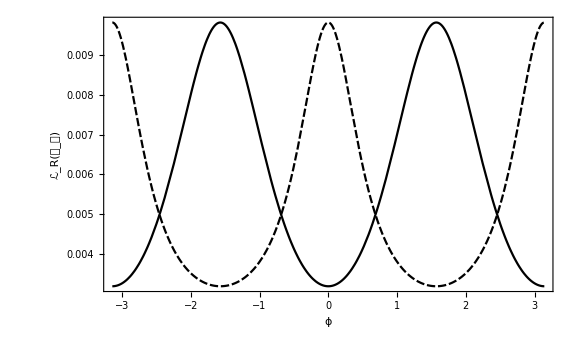

```mathematica
nμ0=0.1;
nσ0=0.1;

np0=0.1;
nVxx=0.5;
nVpp=0.5;

x0list={0.1,1};

Plot[{MSL1xϕxϕ2[ϕ,nμ0,nσ0,10,0,nVxx,nVpp],MSL1xϕxϕ2[ϕ,nμ0,nσ0,0,10,nVxx,nVpp]},{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,0,π/2}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

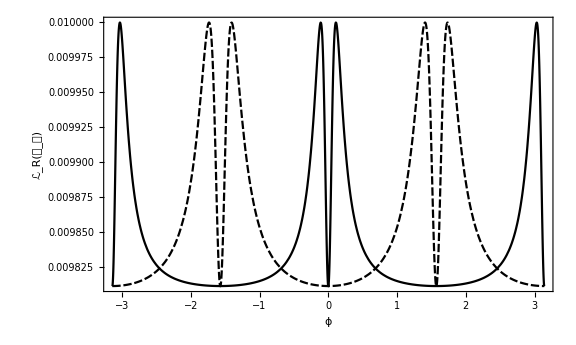

```mathematica
nx0=0.01;
np0=0.01;


Plot[Evaluate[{MSL1xϕxϕ2[ϕ,nμ0,nσ0,nx0,np0,0.5*Exp[-r],0.5*Exp[r]],MSL1xϕxϕ2[ϕ,nμ0,nσ0,nx0,np0,0.5*Exp[r],0.5*Exp[-r]]}/.{r->2}],{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,0,π/2,-π/4,π/4}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

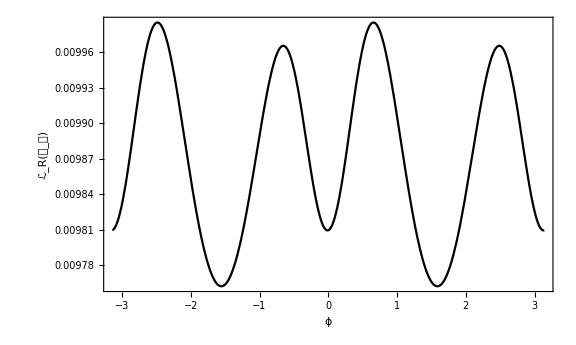

```mathematica
Plot[{MSL1xϕxϕ2[ϕ,nμ0,nσ0,0.1,0.5,nVxx,nVpp]},{ϕ,-π,π},PlotRange->All,GridLines->{{-π/2,0,π/2}, {}},Axes->False,AspectRatio->0.6,PlotTheme->"Monochrome",Frame->True,LabelStyle->Directive["Helvetica", 14],FrameLabel->{ϕ,"ℒ_R(𝒮_𝒱)"},ImageSize->Large]
```

### B={1,Δx^2}

```mathematica
Gxx=Integrate[(Expand[(x)^2]) p[θ]/.{x^2->Exp[-2 θ](x0^2+Vxx) ,x->x0*Exp[-θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

Gx2x2=Integrate[(Expand[(x)^4]) p[θ]/.{x^4->Exp[-4θ](x0^4+6*x0^2*Vxx+3*Vxx^2),x^3->Exp[-3θ](x0^3+3*x0*Vxx),x^2->Exp[-2 θ](x0^2+Vxx),x->x0*Exp[- θ]},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify


(*Build Gram matrix block*)
Gmat=({{1, Gxx}, {Gxx, Gx2x2}});

Gmat//MatrixForm
```

ⅇ^(-2 μ0+2 σ0^2) (Vxx+x0^2)

ⅇ^(-4 μ0+8 σ0^2) (3 Vxx^2+6 Vxx x0^2+x0^4)

(1 | ⅇ^(-2 μ0+2 σ0^2) (Vxx+x0^2)
ⅇ^(-2 μ0+2 σ0^2) (Vxx+x0^2) | ⅇ^(-4 μ0+8 σ0^2) (3 Vxx^2+6 Vxx x0^2+x0^4))

```mathematica
(*Subscript[b, i]= <Subscript[B, i]>_(ρ̄)*)
b0=Integrate[θ p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0];
bx=Integrate[θ(x^2) p[θ]/.{x^2->Exp[-2 θ](x0^2+Vxx)},{θ,-Infinity,Infinity},Assumptions->σ0>0]//Simplify

bvec={b0,bx};
bvec//Simplify

(*Solve*)
alpha=Simplify[Inverse[Gmat].bvec]//Simplify
(*Small sigma expansion*)
alphaSeries=Normal[Series[alpha,{σ0,0,2}]]


λ=Integrate[θ^2 p[θ],{θ,-Infinity,Infinity},Assumptions->σ0>0];

MSL=λ-bvec.Inverse[Gmat].bvec//FullSimplify
```

ⅇ^(-2 μ0+2 σ0^2) (Vxx+x0^2) (μ0-2 σ0^2)

{μ0,ⅇ^(-2 μ0+2 σ0^2) (Vxx+x0^2) (μ0-2 σ0^2)}

{(x0^4 ((-1+ⅇ^(4 σ0^2)) μ0+2 σ0^2)+Vxx^2 ((-1+3 ⅇ^(4 σ0^2)) μ0+2 σ0^2)+2 Vxx x0^2 ((-1+3 ⅇ^(4 σ0^2)) μ0+2 σ0^2))/((-1+3 ⅇ^(4 σ0^2)) Vxx^2+2 (-1+3 ⅇ^(4 σ0^2)) Vxx x0^2+(-1+ⅇ^(4 σ0^2)) x0^4),-(2 ⅇ^(2 μ0-2 σ0^2) (Vxx+x0^2) σ0^2)/((-1+3 ⅇ^(4 σ0^2)) Vxx^2+2 (-1+3 ⅇ^(4 σ0^2)) Vxx x0^2+(-1+ⅇ^(4 σ0^2)) x0^4)}

{μ0+((Vxx+x0^2)^2 σ0^2)/(Vxx (Vxx+2 x0^2)),-(ⅇ^(2 μ0) (Vxx+x0^2) σ0^2)/(Vxx (Vxx+2 x0^2))}

(σ0^2 (ⅇ^(4 σ0^2) (3 Vxx^2+6 Vxx x0^2+x0^4)-(Vxx+x0^2)^2 (1+4 σ0^2)))/(-(Vxx+x0^2)^2+ⅇ^(4 σ0^2) (3 Vxx^2+6 Vxx x0^2+x0^4))

```mathematica
Normal[Series[MSL/.x0->0,{σ0,0,4}]]
```

σ0^2-2 σ0^4

## Symmetric logarithmic derivative (SLD)

We want to obtain the symmetric logarithmic derivative. For a Gaussian state, it is a quadratic form of position and momentum (x and p) 

ℒ=∑_ij L_ij 1/2{R_i-d_i,R_j-d_j}_++∑_i b_i(R_i-d_i)-1/2 tr{L Γ},

here, d_i=⟨R_i⟩=tr{R_i ρ}, R⃗=(x,p), Γ=2σ and σ_ij=1/2⟨{R_i,R_j}_+⟩ are the elements of the (symmetrized) covariance matrix. See Monras (2013) https://arxiv.org/pdf/1303.3682.

Here, Ω=(0 | -1
1 | 0) is the symplectic matrix. 

The coefficients are given by

L=𝒟_Γ^-1(∂Γ)
b⃗=2 Γ^-1∂d⃗,

where the application 𝒟_Γ(Y)=Γ Y Γ^T-Ω Y Ω^T, and ∂ is a shorthand for ∂/∂θ. Hence, 𝒟_Γ^-1(∂Γ) is the solution Y to the matrix equation

∂Γ=Γ Y Γ^T-Ω Y Ω^T
Ω^-1∂Γ (Ω^T)^-1=Ω^-1 Γ Y (Γ^T(Ω^T))^-1-Y
Ω^T∂Γ Ω=(Ω^T Γ)(Y(Ω^T Γ))^T-Y
Y-F Y F^T=-Ω^T∂Γ Ω.

In our case, we have

```mathematica
covSqueezed[θ_]:=({{Vxx*Exp[-2θ], Vxp}, {Vxp, Vpp*Exp[2θ]}})
```

```mathematica
mL=({{L[1,1], L[1,2]}, {L[2,1], L[2,2]}});
Γ=2covSqueezed[θ];
dΓ=D[2covSqueezed[θ],θ]//FullSimplify;
Ω=({{0, -1}, {1, 0}});
F=Transpose[Ω].Γ;
```

```mathematica
sol=Solve[Flatten[mL-F.mL.Transpose[F]]⟦#⟧==Flatten[-Transpose[Ω].dΓ.Ω]⟦#⟧&/@Range[4],Flatten[mL]]//FullSimplify;mL/.Flatten[sol]//MatrixForm//TraditionalForm
```

(-(4 ⅇ^(2 θ) Vpp)/(4 Vpp Vxx-4 Vxp^2+1) | 0
0 | (4 ⅇ^(-2 θ) Vxx)/(4 Vpp Vxx-4 Vxp^2+1))

Note that Y-F Y F^T=-Ω^T∂Γ Ω is a discrete-time Lyapunov equation, whose solution is formally given by Y = -∑_k F^k(Ω^T∂Γ Ω)F^(T k).

```mathematica
-Sum[FullSimplify[MatrixPower[F,k].Transpose[Ω].dΓ.Ω.MatrixPower[Transpose[F],k],Assumptions->{k∈Integers,k>0}],{k,0,Infinity}]//MatrixForm//TraditionalForm
```

(-(4 ⅇ^(2 θ) Vpp)/(4 Vpp Vxx-4 Vxp^2+1) | 0
0 | (4 ⅇ^(-2 θ) Vxx)/(4 Vpp Vxx-4 Vxp^2+1))

The linear term b⃗=2 Γ^-1∂d⃗ is

```mathematica
Inverse[Γ].D[2{x0*Exp[-θ],p0*Exp[θ]},θ]//FullSimplify
```

{-(ⅇ^θ x0)/Vxx,(ⅇ^-θ p0)/Vpp}

The linear part of the QFI is then

```mathematica
Clear[x,p]
```

```mathematica
Expand[({-(ⅇ^θ x0)/Vxx,(ⅇ^-θ p0)/Vpp}.({x,p}-{x0*Exp[-θ],p0*Exp[θ]}))^2]/.{x^2->Exp[-2θ]*(x0^2+Vxx),x->x0*Exp[-θ],p^2->Exp[2θ]*(p0^2+Vpp),p->p0*Exp[θ]}//Simplify
```

p0^2/Vpp+x0^2/Vxx

The constant term is -1/2tr{L Γ}=0 in our case

```mathematica
-1/2 Tr[(mL/.Flatten[sol]).Γ]
```

0

The quadratic part of the QFI is

```mathematica
1/2(mL/.Flatten[sol]).dΓ//Diagonal//Total//Simplify
```

(16 Vpp Vxx)/(1-4 Vxp^2+4 Vpp Vxx)

```mathematica
(*This matches the MSL of for the quadratic basis {1,x^2,p^2}*)
Normal[Series[MSL,{σ0,0,4}]]
```

σ0^2-(16 Vpp Vxx σ0^4)/(1-4 Vxp^2+4 Vpp Vxx)